# EIWL Sections 43 (no problems) and 44

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

# Chapter 44

```mathematica
Import["https://google.com","Images"]
```

{-Graphics-}

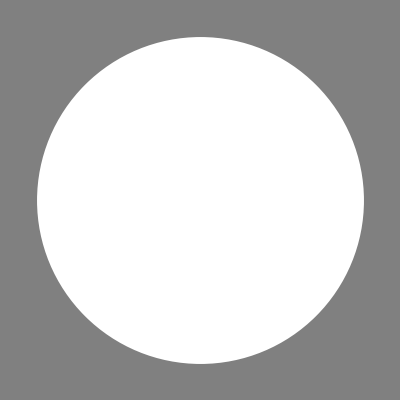
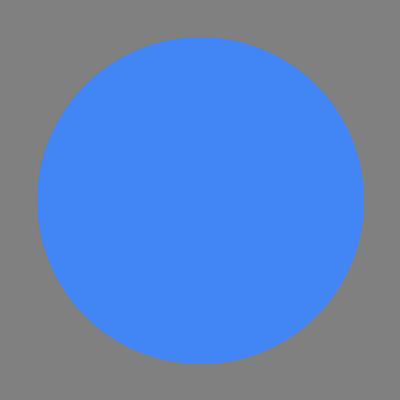
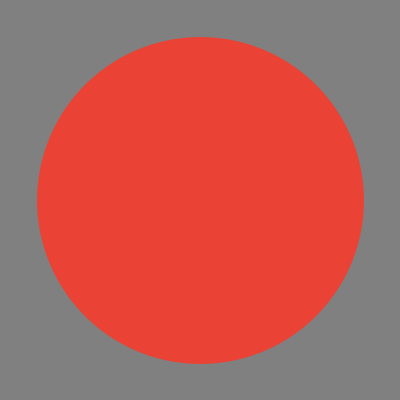
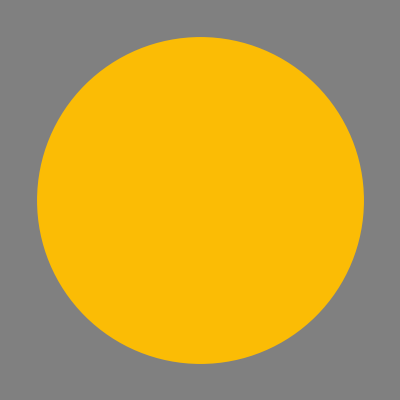
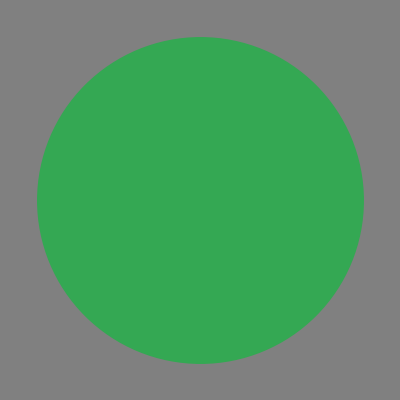

```mathematica
Graphics[Style[Disk[],#],Background->Gray]&/@(Flatten[DominantColors/@Import["https://google.com","Images"]])
```

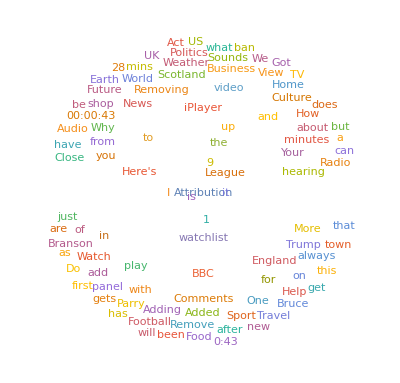

```mathematica
WordCloud[TextWords[Import["https://bbc.co.uk"]]]
```

```mathematica
ImageCollage[Import["https://www.nps.gov","Images"]]
```

Import::htmlimg: Some images could not be imported.

ImageCollage::invarg: {} should be a list of images, a list of rules weight -> image, or a rule weights -> images.

ImageCollage[{}]

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,Entity["TaxonomicSpecies","Aves::m4h27"]]&]
```

Import::htmlimg: Some images could not be imported.

ImageInstanceQ::objinv: birds is not a known object or an Alternative between known objects.

General::stop: Further output of ImageInstanceQ::objinv will be suppressed during this calculation.

{}

FetchURL::conopen: The connection to URL https://.int/ cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

TextCases::nlpstrfile: String, File, ContentObject or non-empty list of these textual objects expected for the text at position 1.

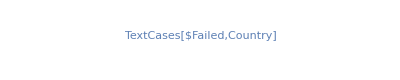

```mathematica
WordCloud[TextCases[Import["https://.int/"],"Country"]]
```

```mathematica
Length[Import["https://en.wikipedia.org","Hyperlinks"]]
```

362

```mathematica
SendMail[GeoGraphics["Deep Springs College"]]
```

Failure[PlanRestrictionFailure]

```mathematica
SendMail[MoonPhase["Icon"]]
```

Failure[PlanRestrictionFailure]